## Calculus III Lab #3: Vector-valued functions

### Let' s define a vector - valued function for the sine curve.

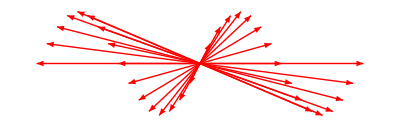

```mathematica
x[t_]:=t
y[t_]:=2Sin[t]
vectorvalue = Table[Arrow[{{0,0},{x[t],y[t]}}],{t,-2π,2π,π/8}];
a1=Show[Graphics[{RGBColor[1,0,0],vectorvalue}],AspectRatio->Automatic]
```

### Now let' s do the velocity vectors.

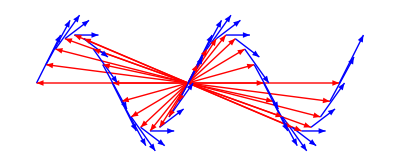

```mathematica
velvector = Table[Arrow[{{x[t],y[t]},{x[t]+x'[t],y[t]+y'[t]}}],{t,-2π,2π,π/8}];
a2=Show[Graphics[{RGBColor[0,0,1],velvector}],AspectRatio->Automatic];
Show[a1,a2]
```

### Exercises Lab #3

### 1. Define vector - valued function r⃗( t ) = < 4cos( t ), 2sin( t ) >. Graph the velocity and acceleration vectors on the same graph as above.

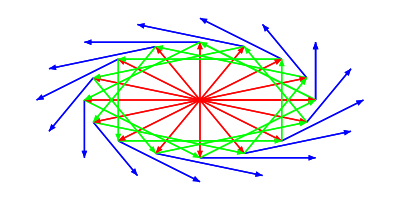

```mathematica
x[t_]:=4Cos[t]
y[t_]:=2Sin[t]
vectorvalue = Table[Arrow[{{0,0},{x[t],y[t]}}],{t,-2π,2π,π/8}];
a1=Show[Graphics[{RGBColor[1,0,0],vectorvalue}],AspectRatio->Automatic];
velvector = Table[Arrow[{{x[t],y[t]},{x[t]+x'[t],y[t]+y'[t]}}],{t,-2π,2π,π/8}];
a2=Show[Graphics[{RGBColor[0,0,1],velvector}],AspectRatio->Automatic];
accelvector = Table[Arrow[{{x[t],y[t]},{x[t]+x'[t]+ x''[t],y[t]+y'[t]+ y''[t]}}],{t,-2π,2π,π/8}];
a3=Show[Graphics[{RGBColor[0,1,0],accelvector}],AspectRatio->Automatic];
Show[a1,a2, a3]
```

### 2. Use the above function and find its unit tangent vector, T^∧( t ), and the principal unit normal vector, N^∧( t ). Plot these with r⃗( t ) on the same graph.

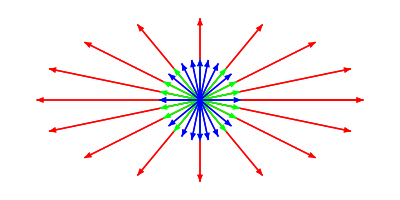

```mathematica
r[t_] := {4Cos[t], 2Sin[t]}
vectorvalue = Table[Arrow[{{0,0},r[t]}],{t,-2π,2π,π/8}];
a1=Show[Graphics[{RGBColor[1,0,0],vectorvalue}],AspectRatio->Automatic];
uT[t_]:=Simplify[r'[t]/Norm[r'[t]],t∈Reals]
tvalue = Table[Arrow[{{0,0},uT[t]}],{t,-2π,2π,π/8}];
a2=Show[Graphics[{RGBColor[0,1,0],tvalue}],AspectRatio->Automatic];
vN[t_]:=Simplify[uT'[t]/Norm[uT'[t]],t∈Reals];
nvalue = Table[Arrow[{{0,0},vN[t]}],{t,-2π,2π,π/8}];
a3=Show[Graphics[{RGBColor[0,0,1],nvalue}],AspectRatio->Automatic];
Show[a1,a2,a3]
```

### 3. Define your own vector-valued function. Graph its velocity and acceleration vectors on the same graph.

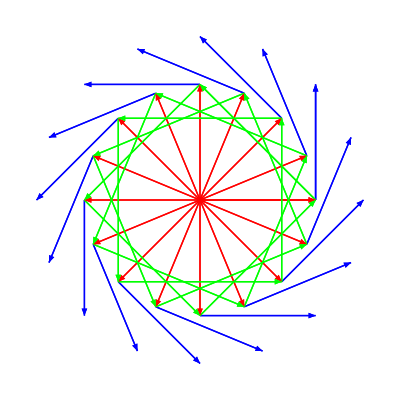

```mathematica
x[t_]:=91Cos[t]
y[t_]:=91Sin[t]
vectorvalue = Table[Arrow[{{0,0},{x[t],y[t]}}],{t,-2π,2π,π/8}];
a1=Show[Graphics[{RGBColor[1,0,0],vectorvalue}],AspectRatio->Automatic];
velvector = Table[Arrow[{{x[t],y[t]},{x[t]+x'[t],y[t]+y'[t]}}],{t,-2π,2π,π/8}];
a2=Show[Graphics[{RGBColor[0,0,1],velvector}],AspectRatio->Automatic];
accelvector = Table[Arrow[{{x[t],y[t]},{x[t]+x'[t]+ x''[t],y[t]+y'[t]+ y''[t]}}],{t,-2π,2π,π/8}];
a3=Show[Graphics[{RGBColor[0,1,0],accelvector}],AspectRatio->Automatic];
Show[a1,a2, a3]
```